```mathematica
ϵ = 1.0;
ϵlj = 2.0;
ϵsm = 3.7/2;
σsm = 0.22272;
σ = 1.0;
Δ = 0.0;
rcut = 1.0;
rcutlj=2.0;
Vslj[r_]:=4ϵ((σ/(r-Δ))^12-(σ/(r-Δ))^6);
Vsljsh[r_]:= Piecewise[{{Vslj[r]-Vslj[rcut+Δ],r<rcut+Δ},{0,r≥rcut+Δ}}]
```

```mathematica
σlj = 1.0;
```

```mathematica
Vlj[r_]:= 4ϵlj((σlj/r)^12-(σlj/r)^6);
Vljsm[r_]:=4 ϵsm((σsm/r)^12-(σsm/r)^6);
Vljsh[r_]:=Piecewise[{{Vlj[r]-Vlj[rcutlj],r<rcutlj},{0,r≥rcutlj}}]
Vljsmsh[r_]:=Piecewise[{{Vljsm[r]-Vljsm[rcutlj],r<rcutlj},{0,r≥rcutlj}}]
```

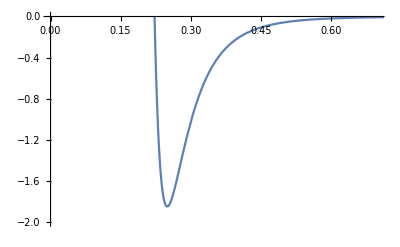

```mathematica
Plot[Vljsm[r],{r,0,5},PlotRange->{{0,0.7},{-2,0.0004}}]
```

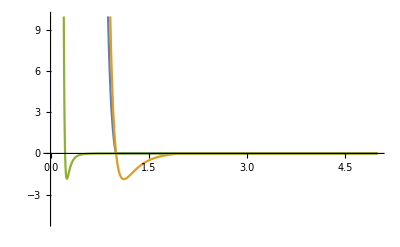

```mathematica
Plot[{Vsljsh[r],Vljsh[r],Vljsm[r]},{r,0,5},PlotRange->{{0,5},{-5,10}}]
```

```mathematica
Vslj[rcut]
```

0.

```mathematica
Vslj[1.1]
```

-0.983372

```mathematica
Vslj[1]
```

0.

```mathematica
Vslj[1.1]
```

-0.983372